## Initialization

```mathematica
Unprotect["Global`*"]
Clear["Global`*"]
ClearAll["Global`*"] 
Remove["Global`*"] 
<<Notation`
Off[Symbolize::bsymbexs]
Off[Remove::rmnsm]

AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]])

Print["Variable Cleared"]

AutoCollapse[]
```

{}

Remove::rmnsm: There are no symbols matching "Global`*".

Variable Cleared

```mathematica
Symbolize[Subscript[u, ρ]]; Symbolize[Subscript[u, ϕ]]; Symbolize[Subscript[u, ζ]]; 
Symbolize[Subscript[u, a]^ρ];Symbolize[Subscript[u, a]^ϕ];Symbolize[Subscript[u, a]^ζ];
Symbolize[u^ρ]; Symbolize[u^ϕ]; Symbolize[u^ζ];
Symbolize[w^ρ]; Symbolize[w^ϕ]; Symbolize[w^ζ];
Symbolize[Subscript[w, ρ]]; Symbolize[Subscript[w, ϕ]]; Symbolize[Subscript[w, ζ]];
 Symbolize[N^𝔄]Symbolize[N^𝔅]Symbolize[N^ℭ];Symbolize[N^𝔇]Symbolize[N^𝔈]Symbolize[N^𝔉];
Symbolize[Subscript[a, ρ,𝔄]];Symbolize[Subscript[a, ϕ,𝔅]];Symbolize[Subscript[a, ζ,ℭ]];
Symbolize[Subscript[b, ρ,𝔇]];Symbolize[Subscript[b, ϕ,𝔈]];Symbolize[Subscript[b, ζ,𝔉]]
Symbolize[L̄];
 Notation[g_(i_·j_·)   ⟺  CoVarMetricCoeffs[[i_,j_]]]
Notation[g^(i_·j_·)   ⟺  ContraVarMetricCoeffs[[i_,j_]]]
Notation[Γ_(i_·j_·)^(k_·)   ⟺  Γ[[i_,j_,k_]]]
Notation[w^(i_·)   ⟺  ContraVarDispW[[i_]]]
Notation[u^(i_·)   ⟺  ContraVarDispU[[i_]]]
Notation[u_(i_·)   ⟺  CoVarDispU[[i_]]]
Notation[x^(i_·)   ⟺  Coords[[i_]]]
Notation[w_(j_·)   ⟺  CoVarDispW[[j_]]]
Notation[u^(i_·)|_(j_·)  ⟺  CovariantDU1[i_,j_]]
Notation[u_(i_·)|_(j_·)  ⟺  CovariantDU2[i_,j_]]
Notation[w^(i_·)|_(j_·)  ⟺  CovariantDW1[i_,j_]]
Notation[w_(i_·)|_(j_·)  ⟺  CovariantDW2[i_,j_]]
Notation[γ_(i_·j_·)   ⟺  StrainCovariantU[[i_,j_]]]
Notation[ϵ_(i_·j_·)   ⟺  StrainCovariantW[[i_,j_]]]
Notation[𝔼^(i_·j_·k_·l_·)   ⟺  StiffnessContra[[i_,j_,k_,l_]]]
Notation[(∂u_)/(∂x_)   ⟺  D[u_,x_]]
Notation[τ^(i_·j_·)   ⟺  StressContra[[i_,j_]]]
Symbolize[x_^h];Symbolize[x_^e];
Symbolize[Subscript[u, ρ]^h];Symbolize[Subscript[u, ϕ]^h];Symbolize[Subscript[u, ζ]^h]
Symbolize[Subscript[η, g]];Symbolize[Subscript[n, x_]];
Symbolize[N^(i_)];Symbolize[N_(,x_)^(i_)];Symbolize[Subscript[x_, i_]];Symbolize[(x⃗)^h];
Symbolize[Subscript[u, ρ]^h];Symbolize[Subscript[u, ϕ]^h];Symbolize[Subscript[u, ζ]^h];
Symbolize[(f⃗)_(e,a)]
Symbolize[(J^e)^-1];
Symbolize[x̲];
Print["New Symbols Defined"]
AutoCollapse[]
```

New Symbols Defined

```mathematica
<<HaneeshPackages`
PrntRls={Subscript[u, 1]-> Subscript[u,1],Subscript[u, 2]-> Subscript[u,2],Subscript[u, 3]-> Subscript[u,3],
Subscript[x, 1]-> Subscript[x,1],Subscript[x, 2]-> Subscript[x,2],Subscript[x, 3]-> Subscript[x,3],
u^ρ-> Superscript[u,ρ],u^ϕ-> Superscript[u,ϕ],u^ζ-> Superscript[u,ζ],
Subscript[u, ρ]-> Subscript[u,ρ],Subscript[u, ϕ]-> Subscript[u,ϕ],Subscript[u, ζ]-> Subscript[u,ζ],
N^𝔄-> Superscript[N,𝔄],N^𝔅-> Superscript[N,𝔅],N^ℭ-> Superscript[N,ℭ],
N^𝔇-> Superscript[N,𝔇],N^𝔈-> Superscript[N,𝔈],N^𝔉-> Superscript[N,𝔉],N^(a)-> Superscript[N,"(a)"],N^(b)-> Superscript[N,"(b)"],
Subscript[a, ρ, 𝔄]-> Subscript[a,ρ,𝔄],Subscript[a, ϕ, 𝔅]-> Subscript[a,ϕ,𝔅],Subscript[a, ζ, ℭ]-> Subscript[a,ζ,ℭ],
Subscript[b, ρ, 𝔇]-> Subscript[b,ρ,𝔇],Subscript[b, ϕ, 𝔈]-> Subscript[b,ϕ,𝔈],Subscript[b, ζ, 𝔉]-> Subscript[b,ζ,𝔉],N_(,ζ)^(a)->Subsuperscript[N,",ζ","(a)"],N_(,ρ)^(a)->Subsuperscript[N,",ρ","(a)"],N_(,ζ)^(b)->Subsuperscript[N,",ζ","(b)"],N_(,ρ)^(b)->Subsuperscript[N,",ρ","(b)"],
Subscript[w, ρ]-> Subscript[w,ρ],Subscript[w, ϕ]-> Subscript[w,ϕ],Subscript[w, ζ]-> Subscript[w,ζ],
L̄->Overscript[L,_],Subscript[ΔT, 0]-> Subscript[ΔT,0]
};


GenerateMonoSubSuperscriptRules[]:=Module[{body, ww,zz,xx,yy,Prules1,Prules2,scripts},
body=Join[Alphabet["Greek"],Alphabet[],ToUpperCase[Alphabet[]],ToUpperCase[Alphabet["Greek"]]];
scripts=Join[Table[ToString[i],{i,1,9}],List@ToString[ϕ],Map[ToString,Alphabet["Greek"]]];
xx=Flatten@Outer[StringJoin,Map[ToString,body],{"⎵Subscript⎵"},scripts];
xx=Map[Symbol,xx];
yy=Flatten@Outer[Subscript,body,scripts];
Prules1=Table[xx[[i]]->yy[[i]],{i,1,Length@xx}];


ww=Flatten@Outer[StringJoin,Map[ToString,body],{"⎵Superscript⎵"},scripts];
ww=Map[Symbol,ww];
zz=Flatten@Outer[Superscript,body,scripts];
Prules2=Table[ww[[i]]->zz[[i]],{i,1,Length@xx}];
Join[Prules1,Prules2]]

(*PrntRls=Join[PrntRls,GenerateMonoSubSuperscriptRules[]];*)


Pprint[expri_]:=Module[{expr=expri},
expr/.PrntRls//MatrixForm//pdConv
];

Pprint[expri_,title_]:=Module[{expr=expri},
(title=expr)/.PrntRls//MatrixForm//pdConv
];


Print["Print Subroutines Defined"]
AutoCollapse[]
```

Print Subroutines Defined

```mathematica
Subscript[u, ρ]::usage="Covariant component of the displacement in the g^ρ direction (symbol)";
Subscript[u, ϕ]::usage="Covariant component of the displacement in the g^ϕ direction ";
Subscript[u, ζ]::usage="Covariant component of the displacement in the g^ζ direction ";

λ::usage="Lame constant (double)";
μ::usage="Lame constant (double)";
Subscript[ρ, 0]::usage="inner radius (double)";
Subscript[ρ, 1]::usage="outer radius (double)";
Subscript[ζ, 0]::usage="curvilinear coordinate ζ's lower bound(double)";
Subscript[ζ, 1]::usage="curvilinear coordinate ζ's upper bound(double)";
αΔT::usage="α=Coefficient of thermal expansion; ΔT=Temperature change function";

Subscript[n, el]::usage="\tNumber of Finite Elements";
Subscript[n, np]::usage="Number of Finite Element Nodes";
Subscript[n, dof]::usage="Number of degrees of freedom per node";
Subscript[n, en]::usage="Number of nodes per finite element";
Subscript[n, eq]::usage="Total Number of Equations";
Subscript[n, guass]:: usage="Number of integration points";





(*Data Structure Arrays*)

SetUpIDArray::usage="Call as SetUpIDArray[]. Will return the ID array";
IEN::usage="IEN(a,e) = A\n\n\ta = Local Node Number\n\te = Element Number\n\tA = Global Node Number";
ID::usage="Dimensions[ID]={n_dof,n_np}\n  
ID[i,A]=Piecewise[{{P,, A∈η-η_g}, {0, A∈η-η_g_i}}]
";



<<NDSolve`FEM`
Guass=N@{{1/6,{1/6,1/6}},
{1/6,{2/3,1/6}},{1/6,{1/6,2/3}}};

(N^(1))[r_,s_]=ElementShapeFunction[TriangleElement,1][r,s][[1]];
(N^(2))[r_,s_]=ElementShapeFunction[TriangleElement,1][r,s][[2]];
(N^(3))[r_,s_]=ElementShapeFunction[TriangleElement,1][r,s][[3]];
(N_(,ξ)^(1))[ξ_,η_]=D[(N^(1))[ξ,η],ξ];
(N_(,η)^(1))[ξ_,η_]=D[(N^(1))[ξ,η],η];
(N_(,ξ)^(2))[ξ_,η_]=D[(N^(2))[ξ,η],ξ];
(N_(,η)^(2))[ξ_,η_]=D[(N^(2))[ξ,η],η];
(N_(,ξ)^(3))[ξ_,η_]=D[(N^(3))[ξ,η],ξ];
(N_(,η)^(3))[ξ_,η_]=D[(N^(3))[ξ,η],η];


Print["Nomenclature defined"]
AutoCollapse[]
```

Nomenclature defined

## Problem Formulations: Theory

```mathematica
Γ=Table[0,{i,1,3},{j,1,3},{k,1,3}];
Γ[[;;,;;,1]]={{0,0,0},{0,-ρ,0},{0,0,0}};
Γ[[;;,;;,2]]={{0,1/ρ,0},{1/ρ,0,0},{0,0,0}};
Γ[[;;,;;,3]]={{0,-(L̄)/ρ,0},{-(L̄)/ρ,0,0},{0,0,0}};
Print["Christoffel Symbols Defined"]
AutoCollapse[]
```

Christoffel Symbols Defined

Christoffel Symbols Defined

Christoffel Symbols Defined

```mathematica
CoVarMetricCoeffs={{1,0,0},{0,ρ^2+(L̄)^2,L̄},{0,L̄,1}};
ContraVarMetricCoeffs={{1,0,0},{0,1/ρ^2,-(L̄)/ρ^2},{0,-(L̄)/ρ^2,(ρ^2+(L̄)^2)/ρ^2}};

Print[Style["Covariant Metric Tensor: ",Orange]]
  Table[g_(i·j·),{i,1,3},{j,1,3}]//Pprint
Print[Style["Contravariant Metric Tensor: ",Orange]]
Table[g^(i·j·),{i,1,3},{j,1,3}]//Pprint

AutoCollapse[]
```

Covariant Metric Tensor:

(1 | 0 | 0
0 | (L̄)^2+ρ^2 | L̄
0 | L̄ | 1)

Contravariant Metric Tensor:

(1 | 0 | 0
0 | 1/ρ^2 | -(L̄)/ρ^2
0 | -(L̄)/ρ^2 | ((L̄)^2+ρ^2)/ρ^2)

```mathematica
Coords={ρ,ϕ,ζ};
ContraVarDispU={Subscript[a, ρ,𝔄](N^𝔄)[ρ,ζ],Subscript[a, ϕ,𝔅](N^𝔅)[ρ,ζ],Subscript[a, ζ,ℭ](N^ℭ)[ρ,ζ]}; 
ContraVarDispW={Subscript[b, ρ,𝔇](N^𝔇)[ρ,ζ],Subscript[b, ϕ,𝔈](N^𝔈)[ρ,ζ],Subscript[b, ζ,𝔉](N^𝔉)[ρ,ζ]}; 


(*ContraVarDispU={0,0,Subscript[c, 3]}; 
ContraVarDispW={0,0,Subscript[c, 4]}; 
*)

CoVarDispU=Table[∑_(j=1)^3 (g_(i·j·)u^(j·)),{i,1,3}];
CoVarDispW=Table[∑_(j=1)^3 (g_(i·j·)w^(j·)),{i,1,3}];


Table[x^(i·),{i,1,3}]//Pprint
Table[u_(i·),{i,1,3}]//Pprint
Table[u^(i·),{i,1,3}]//Pprint
Table[w_(i·),{i,1,3}]//Pprint
Table[w^(i·),{i,1,3}]//Pprint
AutoCollapse[]
```

(ρ
ϕ
ζ)

(a_(ρ,𝔄) N^𝔄(ρ,ζ)
((L̄)^2+ρ^2) a_(ϕ,𝔅) N^𝔅(ρ,ζ)+L̄ a_(ζ,ℭ) N^ℭ(ρ,ζ)
L̄ a_(ϕ,𝔅) N^𝔅(ρ,ζ)+a_(ζ,ℭ) N^ℭ(ρ,ζ))

(a_(ρ,𝔄) N^𝔄(ρ,ζ)
a_(ϕ,𝔅) N^𝔅(ρ,ζ)
a_(ζ,ℭ) N^ℭ(ρ,ζ))

(b_(ρ,𝔇) N^𝔇(ρ,ζ)
((L̄)^2+ρ^2) b_(ϕ,𝔈) N^𝔈(ρ,ζ)+L̄ b_(ζ,𝔉) N^𝔉(ρ,ζ)
L̄ b_(ϕ,𝔈) N^𝔈(ρ,ζ)+b_(ζ,𝔉) N^𝔉(ρ,ζ))

(b_(ρ,𝔇) N^𝔇(ρ,ζ)
b_(ϕ,𝔈) N^𝔈(ρ,ζ)
b_(ζ,𝔉) N^𝔉(ρ,ζ))

```mathematica
CovariantDU2[i_,j_]:=((∂u_(i·))/(∂x^(j·))-∑_(k=1)^3 (u_(k·)Γ_(i·j·)^(k·)));
StrainCovariantU=Table[1/2((u_(i·)|_(j·))+(u_(j·)|_(i·))),{i,1,3},{j,1,3}];

CovariantDW2[i_,j_]:=((∂w_(i·))/(∂x^(j·))-∑_(k=1)^3 (w_(k·)Γ_(i·j·)^(k·)));
StrainCovariantW=Table[1/2((w_(i·)|_(j·))+(w_(j·)|_(i·))),{i,1,3},{j,1,3}];

Print["Strain Tensors"]
{Flatten@FullSimplify@Table[γ_(i·j·),{i,1,3},{j,1,3}]//Pprint,Flatten@FullSimplify@Table[ϵ_(i·j·),{i,1,3},{j,1,3}]//Pprint}
AutoCollapse[]
```

Strain Tensors

{(a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)
1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ))
1/2 (L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ))
1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ))
ρ a_(ρ,𝔄) N^𝔄(ρ,ζ)
1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))
1/2 (L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ))
1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))
L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ)),(b_(ρ,𝔇) (∂N^𝔇(ρ,ζ))/(∂ρ)
1/2 (((L̄)^2+ρ^2) b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ρ)+L̄ b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ρ))
1/2 (L̄ b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ρ)+b_(ρ,𝔇) (∂N^𝔇(ρ,ζ))/(∂ζ)+b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ρ))
1/2 (((L̄)^2+ρ^2) b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ρ)+L̄ b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ρ))
ρ b_(ρ,𝔇) N^𝔇(ρ,ζ)
1/2 (((L̄)^2+ρ^2) b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ζ)+L̄ b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ζ))
1/2 (L̄ b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ρ)+b_(ρ,𝔇) (∂N^𝔇(ρ,ζ))/(∂ζ)+b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ρ))
1/2 (((L̄)^2+ρ^2) b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ζ)+L̄ b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ζ))
L̄ b_(ϕ,𝔈) (∂N^𝔈(ρ,ζ))/(∂ζ)+b_(ζ,𝔉) (∂N^𝔉(ρ,ζ))/(∂ζ))}

```mathematica
Clear[StiffnessContra];
StiffnessContra=μ Table[g^(i·r·) g^(j·s·)+g^(i·s·) g^(j·r·)+λ/μ g^(i·j·)g^(r·s·),{i,1,3},{j,1,3},{r,1,3},{s,1,3}];
Print["Stiffness Defined"]
AutoCollapse[]
```

Stiffness Defined

```mathematica
StressContra=Table[∑_(r=1)^3 ∑_(s=1)^3 𝔼^(i·j·r·s·)(γ_(r·s·)-αΔT[ρ,ζ] g_(r·s·)),{i,1,3},{j,1,3}];
Print["Stress Defined"]
AutoCollapse[]
```

Stress Defined

```mathematica
W=FullSimplify@Sum[τ^(i·j·)ϵ_(i·j·),{i,1,3},{j,1,3}];
Print["Strain Energy Density"]
AutoCollapse[]
```

Strain Energy Density

```mathematica
Patt={
 x_[ρ,ζ] Derivative[0,1][(y_)][ρ,ζ],
x_[ρ,ζ] Derivative[1,0][(y_)][ρ,ζ],Derivative[1,0][(x_)][ρ,ζ]Derivative[1,0][(y_)][ρ,ζ],
Derivative[0,1][(x_)][ρ,ζ]Derivative[0,1][(y_)][ρ,ζ],
Derivative[0,1][(x_)][ρ,ζ]Derivative[1,0][(y_)][ρ,ζ]
x_[ρ,ζ] y_[ρ,ζ]};

Print[Style["Global Stiffness Matrix",Orange]]
K=Simplify@Outer[D[W ,#1,#2]&,{Subscript[a, ρ,𝔄],Subscript[a, ϕ,𝔅],Subscript[a, ζ,ℭ]},{Subscript[b, ρ,𝔇],Subscript[b, ϕ,𝔈],Subscript[b, ζ,𝔉]}];
Flatten@Table[Collect[Expand@K[[i,j]],Patt,Simplify],{i,1,3},{j,1,3}]//Pprint
AutoCollapse[]
```

```mathematica
F=Simplify@Map[D[(W /.{Subscript[a, ρ,𝔄]->0,Subscript[a, ϕ,𝔅]->0,Subscript[a, ζ,ℭ]->0}),#]&,{Subscript[b, ρ,𝔇],Subscript[b, ϕ,𝔈],Subscript[b, ζ,𝔉]}];
Print[Style["Global Force Matrix",Orange]]
Flatten@Table[Collect[Expand@F[[i]],Patt,Simplify],{i,1,3}]//Pprint
AutoCollapse[]
```

Global to Local Transformation

```mathematica
K/.((Derivative[0,1][(N^𝔄)])[ρ,ζ] | (Derivative[0,1][(N^𝔅)])[ρ,ζ] | (Derivative[0,1][(N^ℭ)])[ρ,ζ])-> (N_(,ζ)^(a))[ξ,η]/.((Derivative[1,0][(N^𝔄)])[ρ,ζ] | (Derivative[1,0][(N^𝔅)])[ρ,ζ] | (Derivative[1,0][(N^ℭ)])[ρ,ζ])-> (N_(,ρ)^(a))[ξ,η]/.((N^𝔄)[ρ,ζ]| (N^𝔅)[ρ,ζ] | (N^ℭ)[ρ,ζ])->(N^(a))[ξ,η]/.((Derivative[0,1][(N^𝔇)])[ρ,ζ]| (Derivative[0,1][(N^𝔈)])[ρ,ζ] | (Derivative[0,1][(N^𝔉)])[ρ,ζ])-> (N_(,ζ)^(b))[ξ,η]/.((Derivative[1,0][(N^𝔇)])[ρ,ζ]| (Derivative[1,0][(N^𝔈)])[ρ,ζ] | (Derivative[1,0][(N^𝔉)])[ρ,ζ])-> (N_(,ρ)^(b))[ξ,η]/.((N^𝔇)[ρ,ζ]| (N^𝔈)[ρ,ζ] | (N^𝔉)[ρ,ζ])->(N^(b))[ξ,η]
```

```mathematica
AutoCollapse[]
F/.((Derivative[0,1][(N^𝔄)])[ρ,ζ] | (Derivative[0,1][(N^𝔅)])[ρ,ζ] | (Derivative[0,1][(N^ℭ)])[ρ,ζ])-> (N_(,ζ)^(a))[ξ,η]/.((Derivative[1,0][(N^𝔄)])[ρ,ζ] | (Derivative[1,0][(N^𝔅)])[ρ,ζ] | (Derivative[1,0][(N^ℭ)])[ρ,ζ])-> (N_(,ρ)^(a))[ξ,η]/.((N^𝔄)[ρ,ζ]| (N^𝔅)[ρ,ζ] | (N^ℭ)[ρ,ζ])->(N^(a))[ξ,η]/.((Derivative[0,1][(N^𝔇)])[ρ,ζ]| (Derivative[0,1][(N^𝔈)])[ρ,ζ] | (Derivative[0,1][(N^𝔉)])[ρ,ζ])-> (N_(,ζ)^(b))[ξ,η]/.((Derivative[1,0][(N^𝔇)])[ρ,ζ]| (Derivative[1,0][(N^𝔈)])[ρ,ζ] | (Derivative[1,0][(N^𝔉)])[ρ,ζ])-> (N_(,ρ)^(b))[ξ,η]/.((N^𝔇)[ρ,ζ]| (N^𝔈)[ρ,ζ] | (N^𝔉)[ρ,ζ])->(N^(b))[ξ,η]
AutoCollapse[]
```

## Problem Solution: Numerics

### Numerics subroutine:

```mathematica
Subscript[SetUpη, g][Coordinates0_,tol_:0.0001]:=Module[{Coordinates=Coordinates0,Subscript[n, np], Subscript[ρ, i],Subscript[ζ, i],Subscript[η, g]},
Subscript[n, np]=Length@Coordinates;
Subscript[η, g]={{},{},{}};
For[i=1,i<Subscript[n, np],i++,
{Subscript[ρ, i],Subscript[ζ, i]}=Coordinates[[i]];
If[Abs[Subscript[ζ, i]-Subscript[ζ, 0]]≤   tol,AppendTo[Subscript[η, g][[2]],i]; AppendTo[Subscript[η, g][[3]],i]];
];
Subscript[η, g] 
]
```

```mathematica
SetUpIDArray[]:=Module[{P,A,i,ID},
ID=Table[0,{i,1,Subscript[n, dof]},{j,1,Subscript[n, np]}];
P=1;
For[A=1,A≤ Subscript[n, np],A++,
For[i=1,i≤ Subscript[n, dof],i++,
If[!MemberQ[Subscript[η, g][[i]],A],ID[[i,A]]=P;P=P+1,ID[[i,A]]=0];
];
];
ID
]
```

```mathematica
(k^e)[{ξ_,η_},{ρ_,ζ_}]:={{1/ρ^2((1+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ (N_(,ρ)^(a))[ξ,η] (3 ρ (N_(,ρ)^(b))[ξ,η]+(N^(b))[ξ,η])+(N^(a))[ξ,η] (ρ (N_(,ρ)^(b))[ξ,η]+3 (N^(b))[ξ,η])),-(2 (N_(,ζ)^(b))[ξ,η] (N^(a))[ξ,η])/ρ,(N_(,ζ)^(b))[ξ,η] (N_(,ρ)^(a))[ξ,η]+(N_(,ζ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+((N_(,ζ)^(b))[ξ,η] (N^(a))[ξ,η])/ρ},{-(2 (N_(,ζ)^(a))[ξ,η] (N^(b))[ξ,η])/ρ,1/ρ^2(1+ρ^2) ((1+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]),((1+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η])/ρ^2},{(N_(,ζ)^(b))[ξ,η] (N_(,ρ)^(a))[ξ,η]+(N_(,ζ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+((N_(,ζ)^(a))[ξ,η] (N^(b))[ξ,η])/ρ,((1+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η])/ρ^2,((1+3 ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η])/ρ^2}};



(f^e)[{ξ_,η_},{ρ_,ζ_}]:={-((3 λ+2 μ) (ρ (N_(,ρ)^(b))[ξ,η]+(N^(b))[ξ,η]) αΔT[ρ,ζ])/ρ,0,-(3 λ+2 μ) (N_(,ζ)^(b))[ξ,η] αΔT[ρ,ζ]}

τ12[{ξ_,η_},{ρ_,ζ_},{N^(a):_}]:=ρ^-3{{ρ^2 (Subscript[u, a]^ρ λ (N^(a))[ξ,η]+ρ (Subscript[u, a]^ζ λ (N_(,ζ)^(a))[ξ,η]+Subscript[u, a]^ρ (λ+2 μ) (N_(,ρ)^(a))[ξ,η]-(3 λ+2 μ) αΔT[ρ,ζ])),-L̄ Subscript[u, a]^ρ μ ρ (N_(,ζ)^(a))[ξ,η]+Subscript[u, a]^ϕ μ ρ^3 (N_(,ρ)^(a))[ξ,η],μ ρ (Subscript[u, a]^ρ ((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η]+Subscript[u, a]^ζ ρ^2 (N_(,ρ)^(a))[ξ,η])},{-L̄ Subscript[u, a]^ρ μ ρ (N_(,ζ)^(a))[ξ,η]+Subscript[u, a]^ϕ μ ρ^3 (N_(,ρ)^(a))[ξ,η],Subscript[u, a]^ρ (λ+2 μ) (N^(a))[ξ,η]+ρ (Subscript[u, a]^ζ λ (N_(,ζ)^(a))[ξ,η]-2 L̄ Subscript[u, a]^ϕ μ (N_(,ζ)^(a))[ξ,η]+Subscript[u, a]^ρ λ (N_(,ρ)^(a))[ξ,η]-(3 λ+2 μ) αΔT[ρ,ζ]),-L̄ Subscript[u, a]^ρ (λ+2 μ) (N^(a))[ξ,η]+ρ (Subscript[u, a]^ϕ μ ((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η]-L̄ (Subscript[u, a]^ζ (λ+μ) (N_(,ζ)^(a))[ξ,η]+Subscript[u, a]^ρ λ (N_(,ρ)^(a))[ξ,η])+L̄ (3 λ+2 μ) αΔT[ρ,ζ])},{μ ρ (Subscript[u, a]^ρ ((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η]+Subscript[u, a]^ζ ρ^2 (N_(,ρ)^(a))[ξ,η]),-L̄ Subscript[u, a]^ρ (λ+2 μ) (N^(a))[ξ,η]+ρ (Subscript[u, a]^ϕ μ ((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η]-L̄ (Subscript[u, a]^ζ (λ+μ) (N_(,ζ)^(a))[ξ,η]+Subscript[u, a]^ρ λ (N_(,ρ)^(a))[ξ,η])+L̄ (3 λ+2 μ) αΔT[ρ,ζ]),Subscript[u, a]^ρ ((L̄)^2 (λ+2 μ)+λ ρ^2) (N^(a))[ξ,η]-ρ ((L̄)^2+ρ^2) (-Subscript[u, a]^ζ (λ+2 μ) (N_(,ζ)^(a))[ξ,η]-Subscript[u, a]^ρ λ (N_(,ρ)^(a))[ξ,η]+(3 λ+2 μ) αΔT[ρ,ζ])}}


AutoCollapse[]
```

```mathematica
CalculateGuassPoints[e0_]:=Module[{e=e0,P,Q,R,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],GuassPointsSpatial,GuassPointsNatural,GuassWeights,i,Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[ρ, i],Subscript[ζ, i]},
{P,Q,R}=IEN[[;;,e]];
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]}}=((x⃗)^h)[[{P,Q,R}]];
GuassWeights={};
GuassPointsSpatial={};
GuassPointsNatural={};
For[i=1,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]}}=Guass[[i]];
{Subscript[ρ, i],Subscript[ζ, i]}={(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 3],
(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 3]};
AppendTo[GuassPointsSpatial,{Subscript[ρ, i],Subscript[ζ, i]}];
AppendTo[GuassPointsNatural,{Subscript[ξ, i],Subscript[η, i]}];
AppendTo[GuassWeights,Subscript[w, i]];
];
{GuassWeights,GuassPointsNatural,GuassPointsSpatial}
]
```

```mathematica
ElementJacobian[e0_]:=Module[{e=e0,P,Q,R,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],J^e,B^e},
{P,Q,R}=IEN[[;;,e]];
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]}}=((x⃗)^h)[[{P,Q,R}]];
J^e={{-Subscript[x, 1]+Subscript[x, 2],-Subscript[y, 1]+Subscript[y, 2]},{-Subscript[x, 1]+Subscript[x, 3],-Subscript[y, 1]+Subscript[y, 3]}};
(B^e)[ξ_,η_]= Inverse[J^e].({{(N_(,ξ)^(1))[ξ,η], (N_(,ξ)^(2))[ξ,η], (N_(,ξ)^(3))[ξ,η]}, {(N_(,η)^(1))[ξ,η], (N_(,η)^(2))[ξ,η], (N_(,η)^(3))[ξ,η]}});
{Det[J^e],B^e}
]
```

```mathematica
GuassIntegrate[e0_Integer,f0_]:=Module[{e=e0,f=f0,Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[ρ, i],Subscript[ζ, i],ℐ=0,GuassPoints},
GuassPoints=CalculateGuassPoints[e];
For[i=1,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]},{Subscript[ρ, i],Subscript[ζ, i]}}=GuassPoints[[;;,i]];
ℐ+=Subscript[w, i] f[{Subscript[ξ, i],Subscript[η, i]},{Subscript[ρ, i],Subscript[ζ, i]}]
];
ℐ
]
```

```mathematica
ComputeElementStiffnessMatrix[e0_]:=Module[{e=e0,A,B,P,Q, 𝒾,𝒿,a,b,ρ,ζ,ξ,η,j^e,(J^e)^-1,B^e,ℐ=0.0,f},
{j^e,B^e}=ElementJacobian[e];
For[a=1,a≤ Subscript[n, en],a++,
For[b=1,b≤ Subscript[n, en],b++,
A=IEN[[a,e]];
B=IEN[[b,e]];
{(N_(,ρ)^(a))[ξ_,η_],(N_(,ζ)^(a))[ξ_,η_]}=(B^e)[ξ,η][[;;,a]];
{(N_(,ρ)^(b))[ξ_,η_],(N_(,ζ)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];

For[𝒾=1,𝒾≤ Subscript[n, dof],𝒾++,
For[𝒿=1,𝒿≤ Subscript[n, dof],𝒿++,
f[{ξ_,η_},{ρ_,ζ_}]=j^e(k^e)[{ξ,η},{ρ,ζ}][[𝒾,𝒿]]ρ;
ℐ=GuassIntegrate[e,f];
P=ID[[𝒾,A]];Q=ID[[𝒿,B]];
If[P≠0 && Q≠ 0,KMat[[P,Q]]+=ℐ]
];
];
];
];
]
```

```mathematica
ComputeGlobalForceMatrix[e0_]:=Module[{e=e0,B,Q, 𝒿,b,ρ,ζ,ξ,η,j^e,B^e,f},
{j^e,B^e}=ElementJacobian[e];
For[b=1,b≤ Subscript[n, en],b++,
B=IEN[[b,e]];
{(N_(,ρ)^(b))[ξ_,η_],(N_(,ζ)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
For[𝒿=1,𝒿≤ Subscript[n, dof],𝒿++,
f[{ξ_,η_},{ρ_,ζ_}]=j^e(f^e)[{ξ,η},{ρ,ζ}][[𝒿]]ρ;
ℐ=GuassIntegrate[e,f];
ClearAll[f];
Q=ID[[𝒿,B]];
If[ Q≠ 0,fMat[[Q]]+=ℐ]
];
];
]
```

```mathematica
SplitSolution[sol0_]:=Module[{sol=sol0,e,a,i,A,P,UMat},
UMat=SparseArray[{},{Subscript[n, dof],Subscript[n, np]},0.0];
For[e=1,e ≤  Subscript[n, el],e++, 
For[a=1,a≤  Subscript[n, en],a++,
For[i=1,i≤  Subscript[n, dof],i++,
A=IEN[[a,e]];
P=ID[[i,A]];
If[P≠ 0,UMat[[i,A]]=sol[[P]]];
]
]
];
UMat
]
```

### Define Geometry Dimensions and Material Properties

```mathematica
Unprotect[λ,μ,Subscript[ρ, 0],Subscript[ρ, 1],Subscript[ζ, 0],Subscript[ζ, 1],Ω^h,α, αΔT];
λ=1; μ=1; 
Subscript[ρ, 0]=0.25;Subscript[ρ, 1]=1;
Subscript[ζ, 0]=0.0;Subscript[ζ, 1]=0.58;
L̄=1;
αΔT[ρ_,ζ_]=Log[ρ/Subscript[ρ, 0]];
Ω^h=ToElementMesh[Rectangle[{Subscript[ρ, 0],Subscript[ζ, 0]},{Subscript[ρ, 1],Subscript[ζ, 1]}],MaxCellMeasure->0.02,"MeshElementType"->"TriangleElement","MeshOrder"->1];
Protect[λ,μ,Subscript[ρ, 0],Subscript[ρ, 1],Subscript[ζ, 0],Subscript[ζ, 1],Ω^h,α,αΔT];
```

### Create Mesh and Mesh Data Structures

```mathematica
Unprotect[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,ElementMesh,NMat];
(x⃗)^h=(Ω^h)["Coordinates"];
Subscript[n, np]=Length@((x⃗)^h);
IEN=Apply[List,(Ω^h)["MeshElements"],{1}][[1,1]]ᵀ ;
NMat[ξ_,η_]={1-ξ-η,ξ,η};
Subscript[n, en]=Dimensions[IEN][[1]];
Subscript[n, el]=Dimensions[IEN][[2]];
Subscript[n, dof]=3;
Subscript[n, guass]=3;
Subscript[η, g]=Subscript[SetUpη, g][(x⃗)^h] ;
ID=SetUpIDArray[];
Subscript[n, eq]=Max[ID];
(Ω^h)["PointElements"]={PointElement[Table[{i},{i,1,Subscript[n, np]}]]};
Protect[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,ElementMesh, NMat];
```

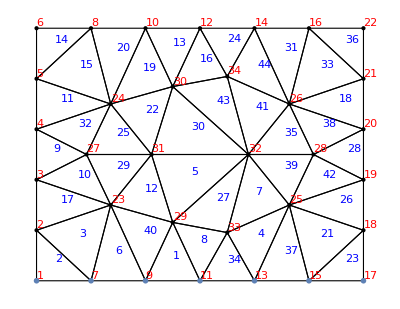

```mathematica
Show[
(Ω^h)["Wireframe"["MeshElement" -> "MeshElements","MeshElementIDStyle"->Blue]],
(Ω^h)["Wireframe"["MeshElement" -> "PointElements","MeshElementIDStyle"->Red]],
ListPlot[((x⃗)^h)[[Subscript[η, g][[3]]]],PlotMarkers->{Green}]]
```

```mathematica
KMat=SparseArray[{},{Subscript[n, eq],Subscript[n, eq]},0.0];
fMat=SparseArray[{},{Subscript[n, eq]},0.0];
For[e=1,e≤ Subscript[n, el],e++, ComputeElementStiffnessMatrix[e];ComputeGlobalForceMatrix[e]]
sol=LinearSolve[KMat,fMat];
UMat=SplitSolution[sol];
{Subscript[Un, 1],Subscript[Un, 2],Subscript[Un, 3]}=Table[ElementMeshInterpolation[{Ω^h}, UMat[[i,;;]]//Normal],{i,1,Subscript[n, dof]}];
```

### Post Processing

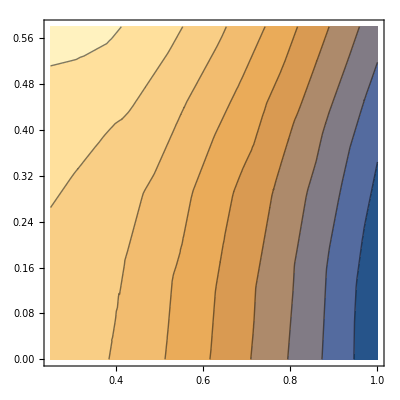

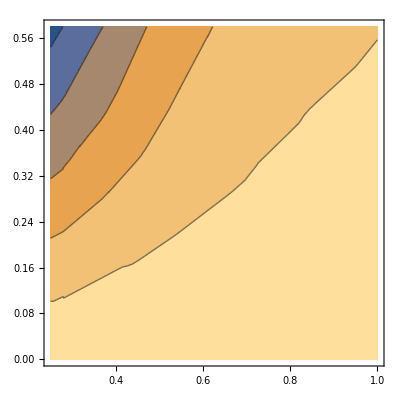

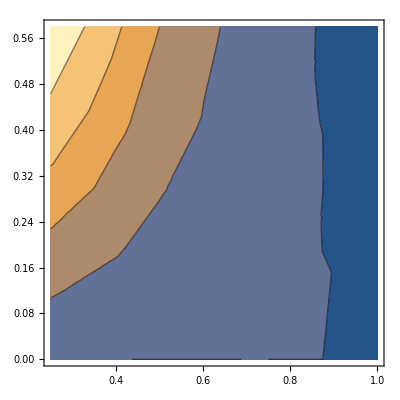

```mathematica
ContourPlot[Subscript[Un, 1][ρ,ζ],{ρ,ζ}∈Ω^h]
ContourPlot[Subscript[Un, 2][ρ,ζ],{ρ,ζ}∈Ω^h]
ContourPlot[Subscript[Un, 3][ρ,ζ],{ρ,ζ}∈Ω^h]
```

```mathematica
R=Simplify@Table[∑_(i=1)^3 D[τ^(i·j·),x^(i·)]+∑_(i=1)^3 ∑_(m=1)^3 Γ_(i·m·)^(i·)τ^(m·j·)+∑_(i=1)^3 ∑_(m=1)^3 Γ_(i·m·)^(j·)τ^(i·m·),{j,1,3}];
```

```mathematica
R[[1]]//Pprint
```

(μ (L̄)^2 a_(ρ,𝔄) (∂^2 N^𝔄(ρ,ζ))/(∂ζ^2))/ρ^2+(2 μ L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ))/ρ+λ a_(ζ,ℭ) (∂^2 N^ℭ(ρ,ζ))/(∂ρ ∂ζ)+μ a_(ζ,ℭ) (∂^2 N^ℭ(ρ,ζ))/(∂ρ ∂ζ)+μ a_(ρ,𝔄) (∂^2 N^𝔄(ρ,ζ))/(∂ζ^2)-((λ+2 μ) a_(ρ,𝔄) N^𝔄(ρ,ζ))/ρ^2+λ a_(ρ,𝔄) (∂^2 N^𝔄(ρ,ζ))/(∂ρ^2)+(λ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ))/ρ+2 μ a_(ρ,𝔄) (∂^2 N^𝔄(ρ,ζ))/(∂ρ^2)+(2 μ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ))/ρ-3 λ (∂αΔT(ρ,ζ))/(∂ρ)-2 μ (∂αΔT(ρ,ζ))/(∂ρ)

0

```mathematica
(N^(1))[ρ,ζ]
```

1-ζ-ρ

```mathematica
(2 μ L̄ Subscript[a, ϕ,𝔅] (∂N^𝔅(ρ,ζ))/(∂ζ))/ρ-((λ+2 μ) Subscript[a, ρ,𝔄] N^𝔄(ρ,ζ))/ρ^2+(λ Subscript[a, ρ,𝔄] (∂N^𝔄(ρ,ζ))/(∂ρ))/ρ+(2 μ Subscript[a, ρ,𝔄] (∂N^𝔄(ρ,ζ))/(∂ρ))/ρ-3 λ (∂αΔT(ρ,ζ))/(∂ρ)-2 μ (∂αΔT(ρ,ζ))/(∂ρ)
```

```mathematica
r1=Rectangle[{0,0},{1,1}]
```

Rectangle[{0,0},{1,1}]

```mathematica
El=GetElement[1];
```

```mathematica
ClearAll[GetElementRegionGivenElementNumber,GetElementMeshGivenElementNumber,GetElementNumberGivenCoordinates];
GetElementRegionGivenElementNumber[e_]:=Module[{𝒜, ℬ, 𝒞,𝒟,Subscript[p, 1],Subscript[p, 2],Subscript[p, 3]},
𝒜=IEN[[1,e]];
ℬ=IEN[[2,e]];
𝒞=IEN[[3,e]];
Subscript[p, 1]=((x⃗)^h)[[𝒜]];
Subscript[p, 2]=((x⃗)^h)[[ℬ]];
Subscript[p, 3]=((x⃗)^h)[[𝒞]];
Triangle[{Subscript[p, 1],Subscript[p, 2],Subscript[p, 3]}]
]

GetElementMeshGivenElementNumber[e_]:=Module[{𝒜, ℬ, 𝒞,Subscript[p, 1],Subscript[p, 2],Subscript[p, 3]},
𝒜=IEN[[1,e]];
ℬ=IEN[[2,e]];
𝒞=IEN[[3,e]];
Subscript[p, 1]=((x⃗)^h)[[𝒜]];
Subscript[p, 2]=((x⃗)^h)[[ℬ]];
Subscript[p, 3]=((x⃗)^h)[[𝒞]];
ToElementMesh["Coordinates"->{Subscript[p, 1],Subscript[p, 2],Subscript[p, 3]},"MeshElements"-> 
{TriangleElement[{{1,2,3}}]}]]


GetElementNumberGivenCoordinates[{ρ_,ζ_}]:=Module[{e,x̲,El},
x̲={ρ,ζ};
e=1;
El=GetElementRegionGivenElementNumber[e];
While[x̲∉El && e< Subscript[n, el],
e++;
El=GetElementRegionGivenElementNumber[e];
];
e
]
```

```mathematica
ClearAll[ComputeContravariantStress];
ComputeContravariantStress[{ρ_,ζ_},i_Integer,j_Integer]:=Module[{e,x̲,El,𝒜,ℬ,𝒞,a},
x̲={ρ,ζ};
e=GetElementNumberGivenCoordinates[x̲];
{j^e,B^e}=ElementJacobian[e];
For[a=1,a≤ Subscript[n, en],a++,
A=IEN[[a,e]];
P=ID[[𝒾,A]];

{(N_(,ρ)^(a))[ξ_,η_],(N_(,ζ)^(a))[ξ_,η_]}=(B^e)[ξ,η][[;;,a]];
{(N_(,ρ)^(b))[ξ_,η_],(N_(,ζ)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];

For[𝒾=1,𝒾≤ Subscript[n, dof],𝒾++,
Subscript[u, a]^ρ=
Subscript[u, a]^ϕ=
Subscript[u, a]^ζ=


f[{ξ_,η_},{ρ_,ζ_}]=j^e(k^e)[{ξ,η},{ρ,ζ}][[𝒾,𝒿]]ρ;
ℐ=GuassIntegrate[e,f];
If[P≠0 && Q≠ 0,KMat[[P,Q]]+=ℐ]
];
];

];
```

Global`e

```mathematica
?Subscript[n, el]
```

Number of Finite Elements

```mathematica
D[x̲,x]
```

0

```mathematica
Subscript[n, el]
```

342

```mathematica
?Break
```

System`Break

Attributes[Break]={Protected}

11

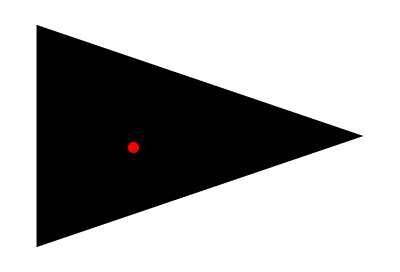

```mathematica
p={0.3,0.4};
e=GetElementNumberGivenCoordinates[p]
Show[Graphics@GetElementRegionGivenElementNumber[e],Graphics[{Red,PointSize[0.02],Point[p]}]]
```

```mathematica
e=GetElementNumberGivenCoordinates[p]
```

11

```mathematica
e=GetElementNumberGivenCoordinates[p]
```

11

```mathematica
p
```

```mathematica
{0.4,0.4}
```